# Ann into q and l

```mathematica
Clear[a]
omega = 6.9*^-9;
mu = 0.105;
abest = 2.87*^-9;
alow = 2.07*^-9;
ahigh = 3.67*^-9;
Ncm = 1;
Ncq = 3;
mldiff = 200;
mqdiff = 800;
gq2f = 0.2;
gq3f = 0.4;
gl2f = 0.4;
```

```mathematica
(*only for g-2; gl,m,Ml*)
tfunc[m_,M_]:=m^2/M^2 (*In Lavoura: t:=m^2/M^2 but elsewhere t=M^2/m^2 when we have two Ms*)
d[t_]:= (-2t^2+7-11)/(18(t-1)^3)+(Log[t])/(3(t-1)^4)
dbar[t_]:=d[t]/t
c[t_]:= (t-3)/(4(t-1)^4)+(Log[t])/(2(t-1)^3) 
cbar[t_]:=-c[t]/t
p[g_,m_]:= g^2*mu^2/(16*Pi^2) * 1/(m+mldiff)^2
```

```mathematica
da[g_,m_,Qf_,Qb_]:=p[g,m]*(Qf*(c[tfunc[m,m+mldiff]]+3/2*d[tfunc[m,m+mldiff]])+ Qb*(-cbar[tfunc[m,m+mldiff]]+3/2*dbar[tfunc[m,m+mldiff]]))
```

```mathematica
(*only for Ann; gl,gq2,gq3,m,Ml,Mq*)
annl[g_,m_,Nc_]:=Nc * g^4/(32*Pi)* m^2/((m+mldiff)^2+m^2)^2;
annq[g1_,g2_,m_,Nc_]:=Nc * (g1^2+g2^2)^2/(32*Pi) * m^2/((m+mqdiff)^2+m^2)^2;
annTot[gl2_,gq2_,gq3_,m_,Nq_,Nl_]:=annl[gl2,m,Nl]+annq[gq2,gq3,m,Nq]
```

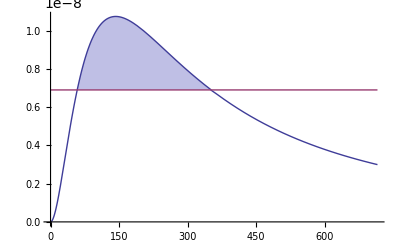

```mathematica
Plot[{annTot[1,0.4,0.4,m,Ncq,Ncm],omega},{m,0,715},Filling->{1->{{2},{None,RGBColor[0.5,0.5,0.8,0.5]}}}]
(*Plot[annl[0.2,m,Ncm],{m,0,1000}]*)
```

```mathematica
test[m_,M_]:=m^2/M^2
alpha[t_]:= t^2-t
```

```mathematica
alpha[test[2,3]]
```

-20/81

-8.31558×10^-10

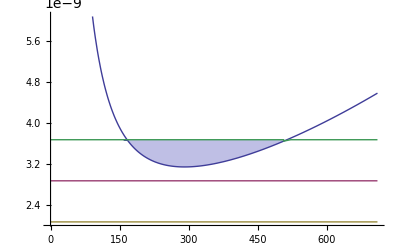

```mathematica
da[1,200,1,0]
(*Plot[c[m],{m,0,1000}]*)
Plot[{(*da[0.4,m,-1,0],da[0.4,m,0,-1],*)da[0.9,m,-1,0]+da[0.9,m,0,-1],abest,alow,ahigh},{m,0,710},Filling->{1->{{4}, {RGBColor[0.5,0.5,0.8,0.5],None}}}]
```